```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY190/sec_int_data/368nm.dat"]
```

{{1.16196,-0.606419},{1.1485,-0.620008},{1.13288,-0.605008},{1.11879,-0.693527},{1.10986,-0.849544},{1.10188,-1.01099},{1.0953,-1.10449},{1.09118,-1.1196},{1.08898,-0.964064},{1.08844,-0.81326},{1.08969,-0.692867},{1.094,-0.607942},{1.09832,-0.584167},{1.10319,-0.55229},{1.11502,-0.582107},{1.13408,-0.538214},{1.14571,-0.577785},{1.16039,-0.561786},{1.17699,-0.5517},{1.19764,-0.581034},{1.21871,-0.593573},{1.24216,-0.602959},{1.26543,-0.608677},{1.29691,-0.610388},{1.32536,-0.661784},{1.37118,-0.672521},{1.45421,-0.736076}}

-1.23606+0.463878 x

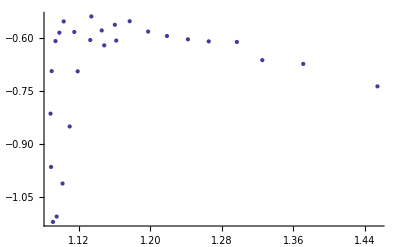

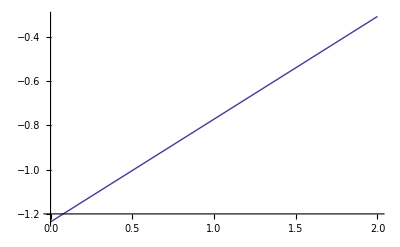

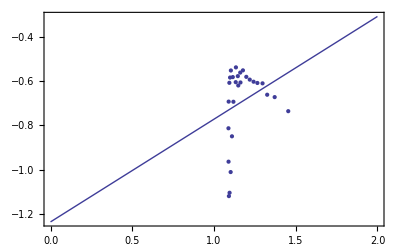

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```